# Karol Peszek - Zestaw 6.

Zadanie A

```mathematica
(*Definicje macierzy A i B*)
A={{1,0},{0,1}};
B={{0,-1},{1,0}};
```

```mathematica
(*Reprezentacja liczby zespolonej x+i y*)
Rep[x_,y_]:=x*A+y*B
```

```mathematica
(*Sprawdzenie:B^2=-A*)
Print["B^2 = ",MatrixPower[B,2]];
Print["-A = ", -1 * A];
```

B^2 = {{-1,0},{0,-1}}

-A = {{-1,0},{0,-1}}

```mathematica
(*Sprawdzenie:reprezentacja dodawania*)
exprAddLeft=Rep[x,y]+Rep[u,v];
exprAddRight=Rep[x+u,y+v];
```

```mathematica
Print["Czy dodawanie zgodne? ",Simplify[exprAddLeft==exprAddRight]];
```

Czy dodawanie zgodne? True

```mathematica
(*Sprawdzenie mnożenia macierzy*)
exprMulLeft=Simplify[Rep[x,y].Rep[u,v]];
exprMulRight=Rep[x*u-y*v,x*v+y*u];
```

```mathematica
Print["Czy mnożenie zgodne z zespolonym? ",exprMulLeft==exprMulRight];
```

Czy mnożenie zgodne z zespolonym? True

```mathematica
(*Sprawdzenie elementu neutralnego 1*)
Print["Rep[1,0] = ",Rep[1,0]];
```

Rep[1,0] = {{1,0},{0,1}}

```mathematica
(*Sprawdzenie odwrotności*)
inv=Simplify[Inverse[Rep[x,y]]];
```

```mathematica
Print["Macierz odwrotna: ",inv];
Print["Czy odwrotność poprawna? ",Simplify[Rep[x,y].inv==A]];
```

Macierz odwrotna: {{x/(x^2+y^2),y/(x^2+y^2)},{-y/(x^2+y^2),x/(x^2+y^2)}}

Czy odwrotność poprawna? True

Zadanie B

```mathematica
Clear["Global`*"]
```

```mathematica
(*Definicje macierzy A i B i reprezentacji liczby zespolonej jak w poprzednim zadaniu*)
A={{1,0},{0,1}};
B={{0,-1},{1,0}};
Rep[x_,y_]:=x A+y B
```

```mathematica
(*Obliczamy wykładniczą macierz exp(phi*B)*)
M=MatrixExp[phi B];
```

```mathematica
(*Wyświetlamy wynik w prostym ujęciu*)
MatrixForm[M]
```

(Cos[phi] | -Sin[phi]
Sin[phi] | Cos[phi])

```mathematica
(*Porównanie z reprezentacją cos phi+i sin phi*)
Target=Rep[Cos[phi],Sin[phi]];
MatrixForm[Target]
```

(Cos[phi] | -Sin[phi]
Sin[phi] | Cos[phi])

```mathematica
(*Sprawdzenie różnicy (powinno dać macierz zerową)*)
Simplify[M-Target]
```

{{0,0},{0,0}}

```mathematica
(*Sprawdzenie równości bezpośrednio (oczekujemy True)*)
Simplify[M==Target]
```

True

```mathematica
(*Dodatkowo:użycie Reduce na równaniu macierzowym*)
Reduce[M==Target,phi,Reals]
```

True

Zadanie C

```mathematica
Clear["Global`*"]
```

```mathematica
(*Dodawanie liczb cn*)
plus[cn[x1_,y1_]][cn[x2_,y2_]]:=cn[x1+x2,y1+y2]
```

```mathematica
(*Mnożenie liczb cn*)
times[cn[x1_,y1_]][cn[x2_,y2_]]:=cn[x1 x2-y1 y2,x1 y2+y1 x2]
```

```mathematica
(*Część rzeczywista*)
re[cn[x_,y_]]:=x
```

```mathematica
(*Część urojona*)
im[cn[x_,y_]]:=y
```

```mathematica
(*Dodawanie i odejmowanie części*)
re[a_+b_]:=re[a]+re[b]
im[a_+b_]:=im[a]+im[b]
```

```mathematica
(*Potęga zerowa to 1*)
power[0][z_]:=cn[1,0]
```

```mathematica
(*Potęga dodatnia–używamy Nest,aby powtarzać mnożenie*)
power[n_Integer?Positive][z_]:=Nest[times[z],cn[1,0],n]
```

```mathematica
(*Potęga ujemna–liczymy dodatnią,a potem odwracamy*)
power[n_Integer?Negative][z_]:=(*liczba zespolona odwrotna:1/z=conj(z)/ |z|^2*)Module[{x=re[z],y=im[z],denom,inv},denom=x^2+y^2;
inv=cn[x/denom,-y/denom];
power[-n][inv]]
```

```mathematica
(*Sprawdzenie,czy działają jak liczby zespolone*)
z1=cn[3,2];
z2=cn[-1,4];
```

```mathematica
Print["z1 + z2 = ",plus[z1][z2]];
Print["z1 * z2 = ",times[z1][z2]];
Print["Dodawanie poprawne?  ",plus[z1][z2]===cn[3-1,2+4]];
Print["Mnożenie poprawne?   ",times[z1][z2]===cn[3*(-1)-2*4,3*4+2*(-1)]];
```

z1 + z2 = cn[2,6]

z1 * z2 = cn[-11,10]

Dodawanie poprawne?  True

Mnożenie poprawne?   True

```mathematica
(*Obliczenie e^i za pomocą szeregu potęgowego*)
(*i jako cn[0,1]*)
z=cn[0,1];
```

```mathematica
(*Obliczamy kolejne wyrazy sumy i^k/k!*)
expApprox=FullSimplify[Sum[(*power[k][z] daje z^k*)With[{zk=power[k][z]},cn[re[zk]/N[Factorial[k]],im[zk]/N[Factorial[k]]]],{k,0,100}]];
```

```mathematica
(*Wyciągamy cos(1) i sin(1)*)
cosApprox=re[expApprox];
sinApprox=im[expApprox];
```

```mathematica
{cosApprox,N[Cos[1]]}
{sinApprox,N[Sin[1]]}
```

{0.540302,0.540302}

{0.841471,0.841471}

Zadanie D

```mathematica
Clear["Global`*"]
```

```mathematica
(*Definicja funkcji zespolonej f(x,y) i rozwiązanie PDE*)
sol=DSolve[{D[f[x,y],y]==I D[f[x,y],x],f[x,0]==Sin[x]},f[x,y],{x,y}]
```

{{f[x,y]→Sin[x+ⅈ y]}}

```mathematica
expr=ComplexExpand[Sin[x+I y]]
```

Cosh[y] Sin[x]+ⅈ Cos[x] Sinh[y]

```mathematica
Simplify[(f[x,y]/. sol)-expr]
```

{0}

```mathematica
(*Wykres*)
fxy=f[x,y]/. sol;
```

```mathematica
u=ComplexExpand[Re[fxy]];   (*część rzeczywista*)
v=ComplexExpand[Im[fxy]];   (*część urojona*)
```

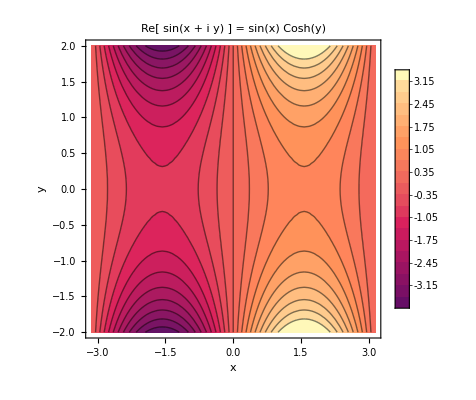

```mathematica
ContourPlot[u,{x,-Pi,Pi},{y,-2,2},FrameLabel->{"x","y"},PlotLegends->Automatic,Contours->20,PlotRange->All,PlotLabel->"Re[ sin(x + i y) ] = sin(x) Cosh(y)"]
```